```mathematica
Show[
Plot[0.5 + ProductLog[x],{x,-1/E,0}, PlotLabels->{"λ_0"}],
Plot[0.5 + ProductLog[-1, x],{x,-1/E ,0},PlotStyle->{Orange}, PlotLabels->{"λ_-1"}],
Graphics[{Red,PointSize -> 0.015,Point[{-1/E,0.5 + ProductLog[-1/E]}]}],
PlotRange->All,
FrameTicks->All,
PlotRangePadding -> 0,
GridLines->Automatic,
GridLinesStyle->Dotted
]
```

-Graphics-

```mathematica
Manipulate[
Show [
Plot[x^2*E^(l/x^2),{x, 1, 5}, PlotStyle->{Red}],
Plot[x^2*E^(-l/x^2),{x, 1, 5}, PlotStyle->{Blue}],
PlotRange->{All, {0,25}},
FrameTicks->All,
PlotRangePadding -> 0,
GridLines->Automatic,
GridLinesStyle->Dotted
],
{{l, 0.371, "λ"}, 0, 2, Appearance -> "Labeled"}
]
```

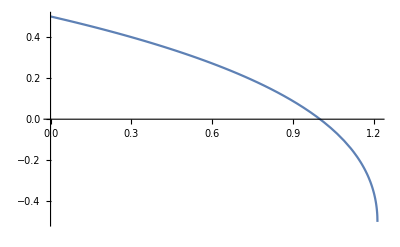

```mathematica
Plot[0.5 + ProductLog[-Om/(2 E^(1/2))], {Om, 0, 2 E^(-1/2)}]
```

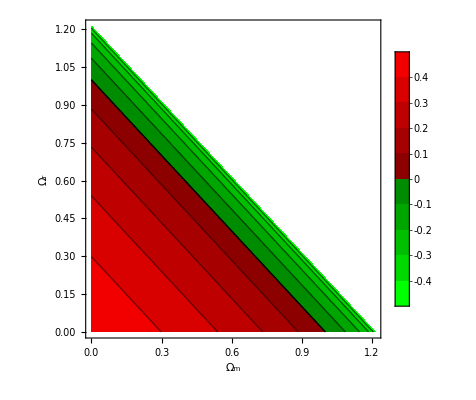

```mathematica
ContourPlot[
0.5 + ProductLog[-(Om+Ora)/(2 E^(1/2))],
{Om,0,2*E^(-1/2)},
{Ora,0,2*E^(-1/2)},
PlotRangePadding -> 0,
FrameLabel -> {"Ω_m","Ω_r"},
PlotLegends->Automatic,
Epilog-> Line[{{0,1},{1,0}},VertexColors -> {Yellow,Yellow}],
ColorFunction->(If[#>.5,RGBColor[#,0,0],RGBColor[0,1-#,0]]&)
]
```